```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","ret/std"},Automatic}]&}
]
```

```mathematica
start5=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
start3=DatePlus[Today,-Quantity[3, "Years"]];
end=Today;
end//DateString
```

Tue 8 Aug 2017

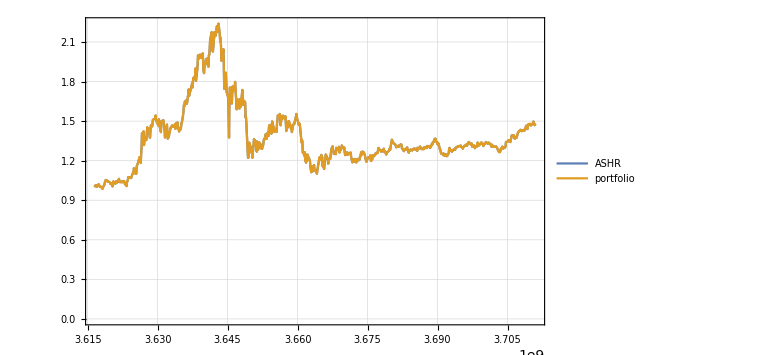
{-Graphics-,return | 1.47769
std | 0.238619
ret/std | 6.19267}

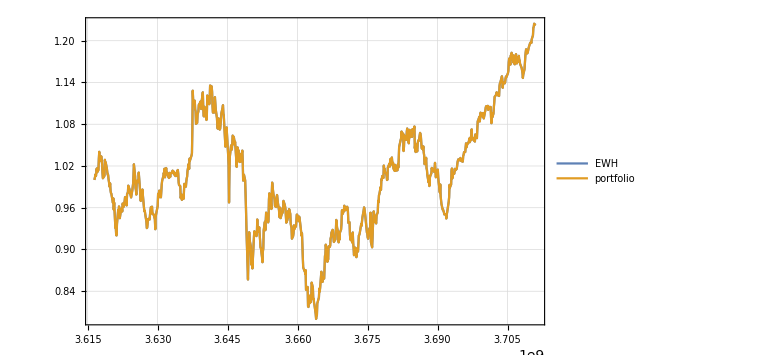
{-Graphics-,return | 1.22255
std | 0.0836637
ret/std | 14.6126}

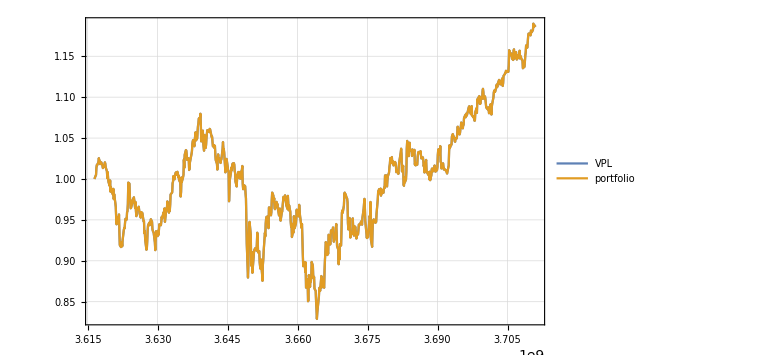
{-Graphics-,return | 1.18791
std | 0.0716189
ret/std | 16.5865}

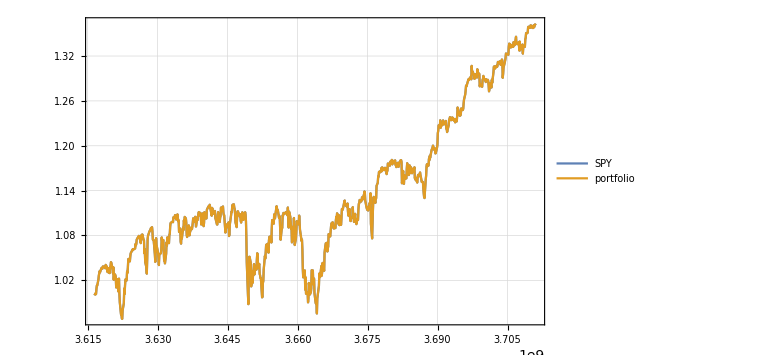
{-Graphics-,return | 1.36328
std | 0.0966041
ret/std | 14.1121}

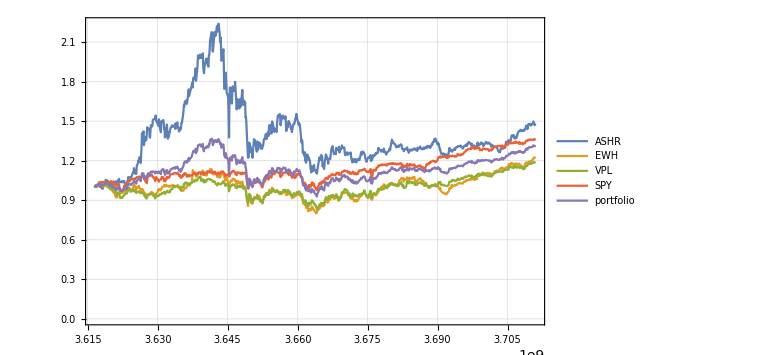
{-Graphics-,return | 1.31286
std | 0.0942303
ret/std | 13.9324}

```mathematica
PortfolioChart[{"ASHR"},start3,end]
PortfolioChart[{"EWH"},start3,end]
PortfolioChart[{"VPL"},start3,end]
PortfolioChart[{"SPY"},start3,end]
PortfolioChart[{"ASHR","EWH","VPL","SPY"},start3,end]
```

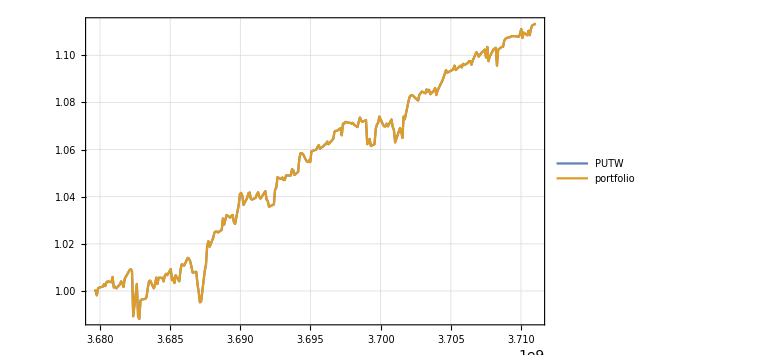
{-Graphics-,return | 1.11342
std | 0.0368056
ret/std | 30.2514}

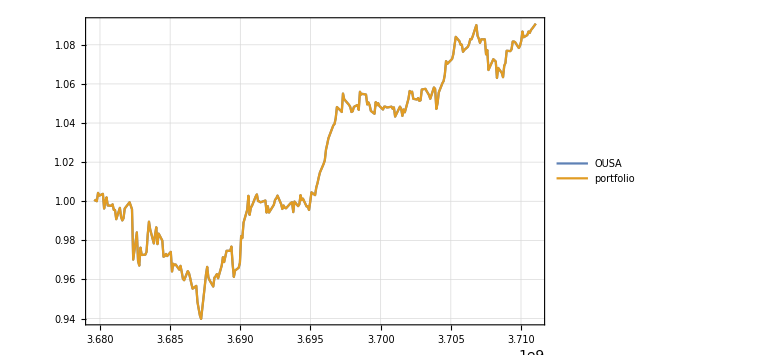
{-Graphics-,return | 1.09082
std | 0.042418
ret/std | 25.7158}

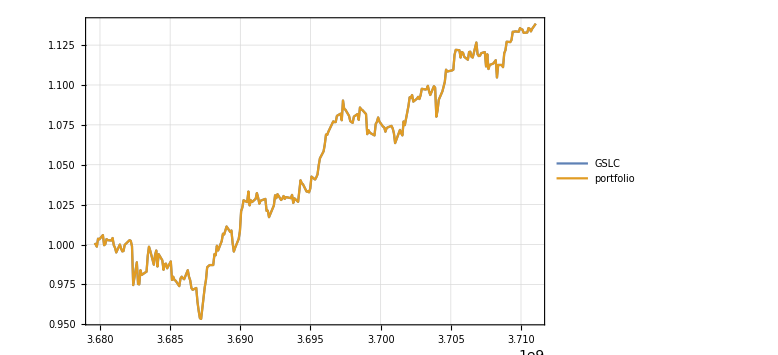
{-Graphics-,return | 1.13844
std | 0.0522291
ret/std | 21.7971}

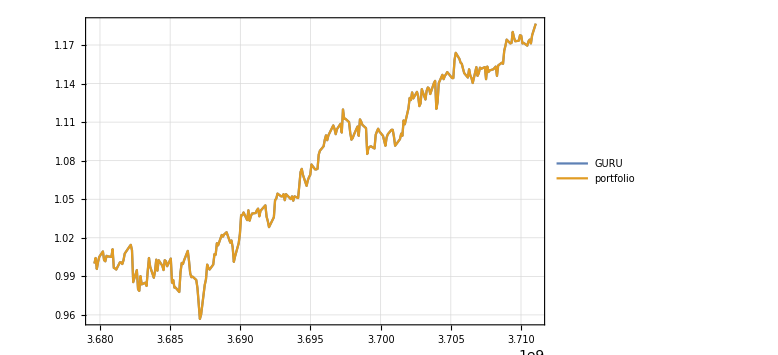
{-Graphics-,return | 1.18661
std | 0.0639747
ret/std | 18.5481}

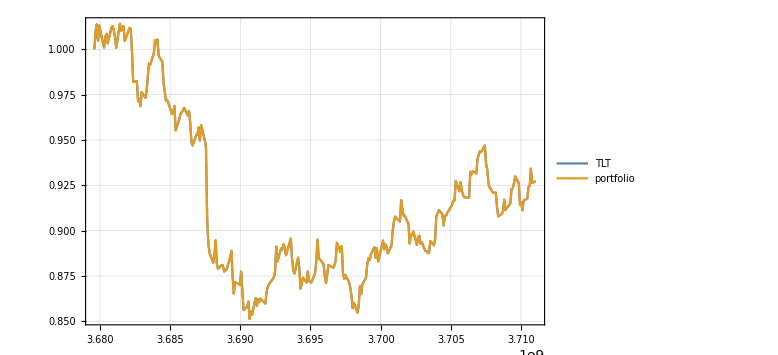
{-Graphics-,return | 0.927311
std | 0.0456861
ret/std | 20.2974}

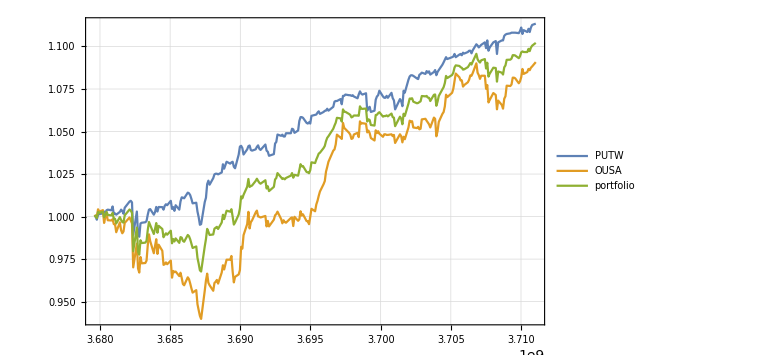
{-Graphics-,return | 1.10212
std | 0.0388205
ret/std | 28.3901}

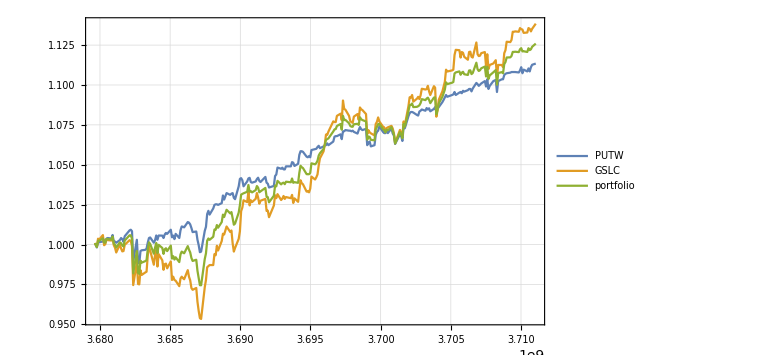
{-Graphics-,return | 1.12593
std | 0.0442532
ret/std | 25.443}

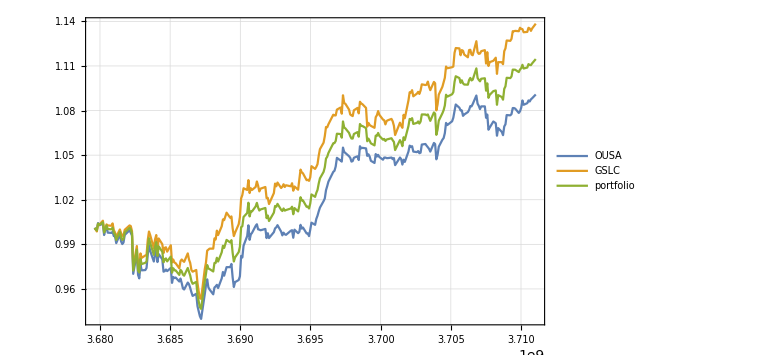
{-Graphics-,return | 1.11463
std | 0.0470801
ret/std | 23.6752}

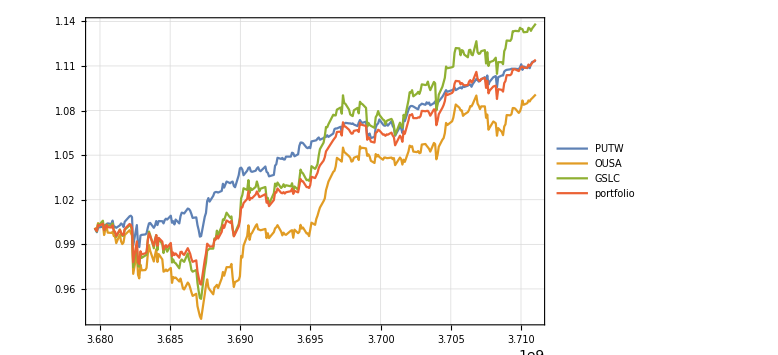
{-Graphics-,return | 1.11423
std | 0.0432638
ret/std | 25.7542}

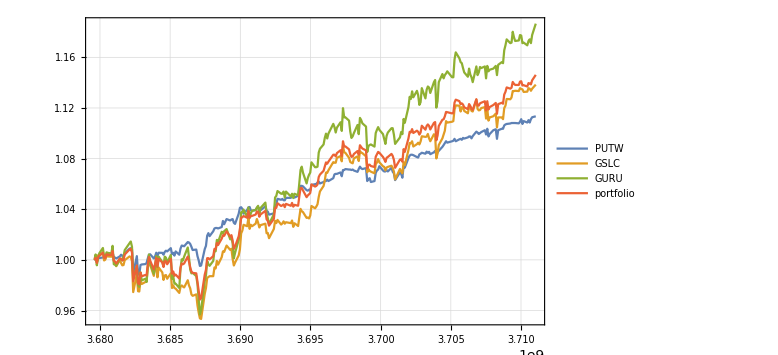
{-Graphics-,return | 1.14616
std | 0.0507785
ret/std | 22.5717}

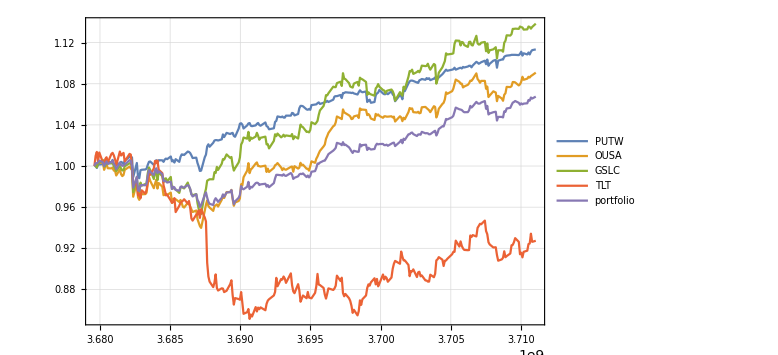
{-Graphics-,return | 1.0675
std | 0.0300399
ret/std | 35.536}

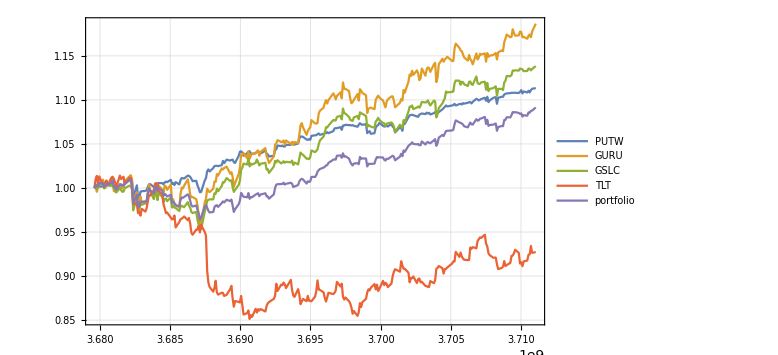
{-Graphics-,return | 1.09145
std | 0.0348119
ret/std | 31.3526}

```mathematica
PortfolioChart[{"PUTW"},start1,end]
PortfolioChart[{"OUSA"},start1,end]
PortfolioChart[{"GSLC"},start1,end]
PortfolioChart[{"GURU"},start1,end]
PortfolioChart[{"TLT"},start1,end]
PortfolioChart[{"PUTW","OUSA"},start1,end]
PortfolioChart[{"PUTW","GSLC"},start1,end]
PortfolioChart[{"OUSA","GSLC"},start1,end]
PortfolioChart[{"PUTW","OUSA","GSLC"},start1,end]
PortfolioChart[{"PUTW","GSLC","GURU"},start1,end]
PortfolioChart[{"PUTW","OUSA","GSLC","TLT"},start1,end]
PortfolioChart[{"PUTW","GURU","GSLC","TLT"},start1,end]
```

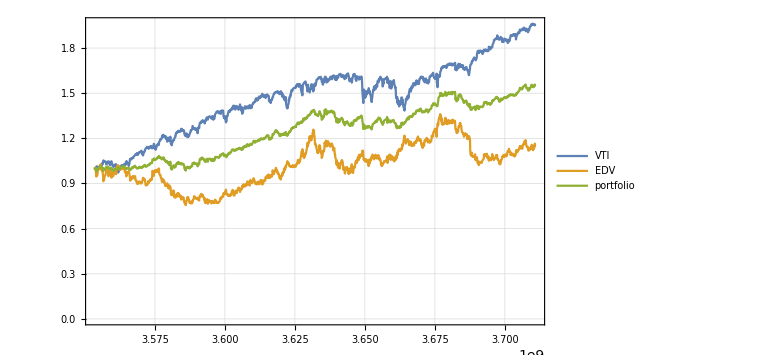
{-Graphics-,return | 1.55568
std | 0.17362
ret/std | 8.96025}

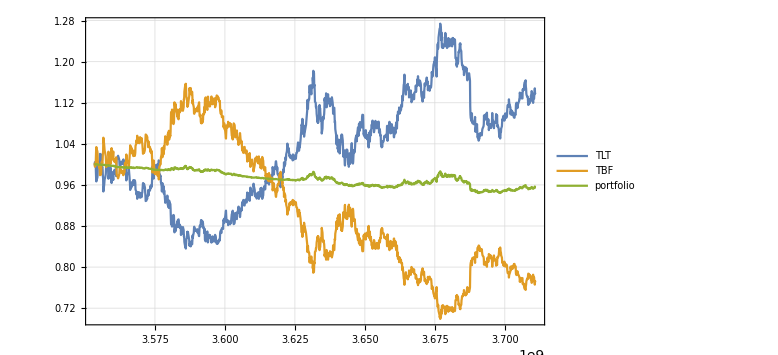
{-Graphics-,return | 0.955313
std | 0.0153035
ret/std | 62.4245}

```mathematica
PortfolioChart[{"VTI","EDV"},start5,end]
PortfolioChart[{"TLT","TBF"},start5,end]
```

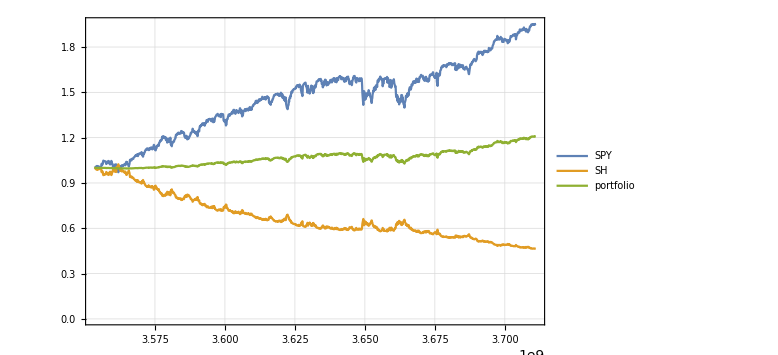
{-Graphics-,return | 1.2097
std | 0.054016
ret/std | 22.3952}

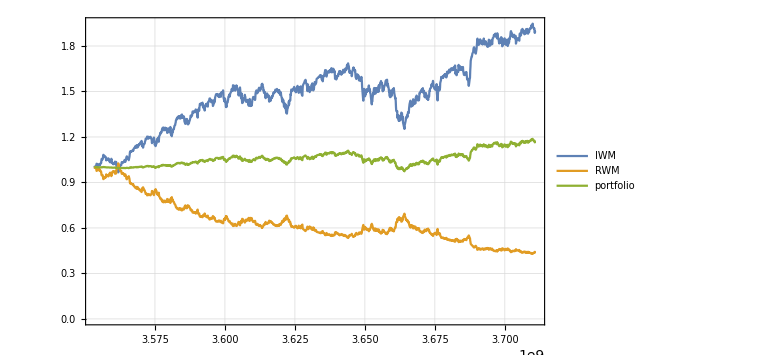
{-Graphics-,return | 1.16898
std | 0.0477722
ret/std | 24.4699}

```mathematica
PortfolioChart[{"SPY","SH"},start5,end]
PortfolioChart[{"IWM","RWM"},start5,end]
```

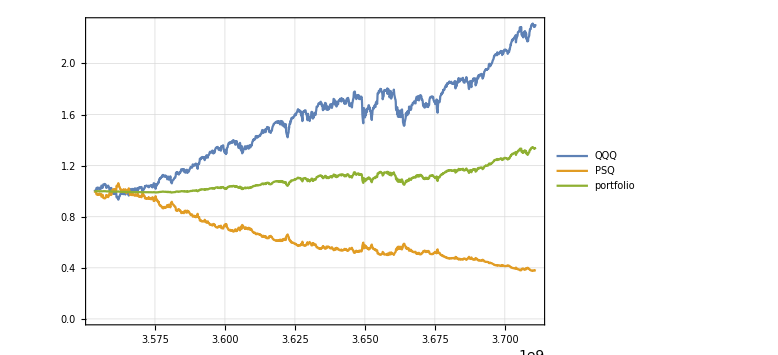
{-Graphics-,return | 1.3421
std | 0.0876501
ret/std | 15.3121}

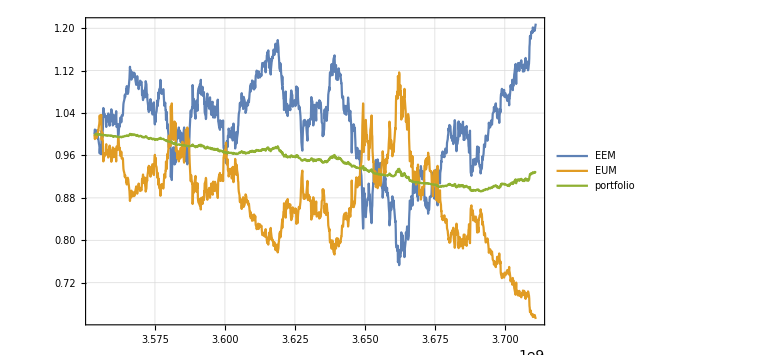
{-Graphics-,return | 0.930179
std | 0.0338096
ret/std | 27.5122}

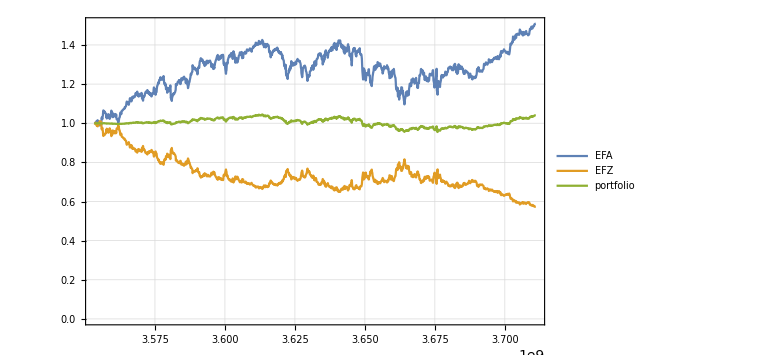
{-Graphics-,return | 1.04118
std | 0.0204138
ret/std | 51.0038}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start5,end]
PortfolioChart[{"EEM","EUM"},start5,end]
PortfolioChart[{"EFA","EFZ"},start5,end]
```

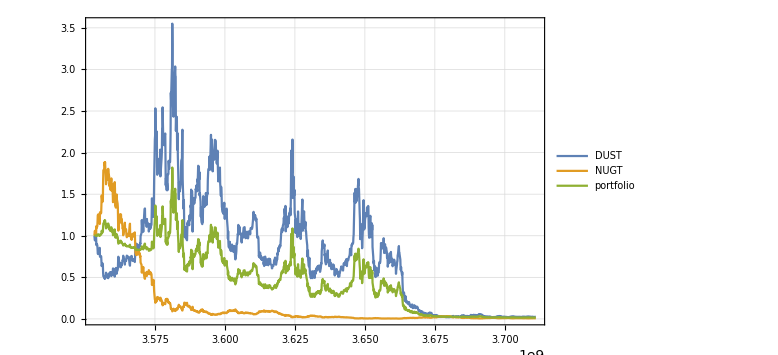
{-Graphics-,return | 0.016466
std | 0.377588
ret/std | 0.0436084}

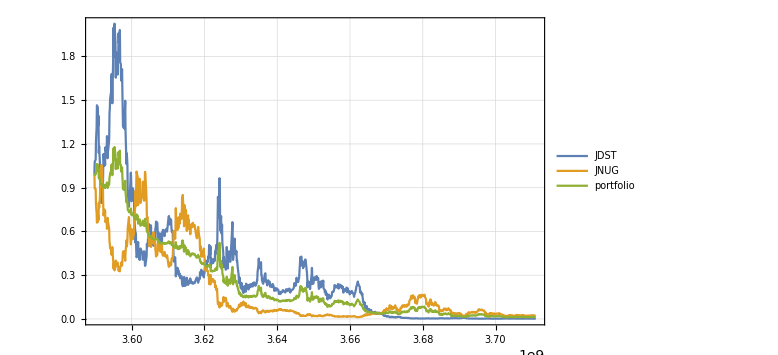
{-Graphics-,return | 0.0118322
std | 0.283307
ret/std | 0.0417644}

```mathematica
PortfolioChart[{"DUST","NUGT"},start5,end]
PortfolioChart[{"JDST","JNUG"},start5,end]
```